## 1.6 Independence

The approach to probability that we have been taking so far draws heavily on random sampling and simulation.  These concepts are also very helpful in understanding the subject of this section: independence of events in random experiments.  For example, what is the crucial difference between sampling five integers in sequence from {1,2, ...,10} without replacement as compared to sampling them with replacement?  In the no replacement scenario, once a number, say 4, is sampled, it cannot appear again, and other numbers are a little more likely to appear later in the sequence because 4 is no longer eligible.  When sampling with replacement, 4 is just as likely to appear again later as it was the first time, and other numbers also have the same likelihood of appearing, regardless of whether 4 was sampled.  In this case, the occurrence of an event like: "4 on 1st" has no effect on the probability of an event like: "7 on 2nd."  This is the nature of independence, and sampling with replacement permits it to happen while sampling without replacement does not. 
	Another way to look at independence involves the computation of intersection probabilities.  Take the example above and use combinatorics to compute the probability that the first two sampled numbers are 4 and 7.  Since we still must account for the other three members of the sample, the probability of this event, assuming no replacement, is

P[4 on 1st, 7 on 2nd] = (1·1·8·7·6)/(10·9·8·7·6) = 1/10·1/9=1/90

The probability of the same event, assuming replacement, is

P[4 on 1st, 7 on 2nd] = (1·1·10·10·10)/(10·10·10·10·10) = 1/10·1/10=1/100

which differs from the answer obtained under the assumption of no replacement.  Moreover, assuming again that the sample is drawn with replacement,

P[4 on 1st] = (1·10·10·10·10)/(10·10·10·10·10) = 1/10 , P[7 on 2nd] = (10·1·10·10·10)/(10·10·10·10·10) = 1/10

hence

P[4 on 1st, 7 on 2nd] = 1/10·1/10= P[4 on 1st]·P[7 on 2nd]

You should check that for sampling without replacement, the joint probability does not factor into the product of individual event probabilities.
	Factorization can occur when three or more events are intersected as well.  For instance when the sample is taken with replacement,

P[4 on 1st, 7 on 2nd, 4 on 3rd] = (1·1·1·10·10)/(10·10·10·10·10) = 1/10·1/10·1/10

P[4 on 1st] = (1·10·10·10·10)/(10·10·10·10·10) = 1/10 = P[7 on 2nd] = P[4 on 3rd]

Therefore,

P[4 on 1st, 7 on 2nd, 4 on 3rd] = P[4 on 1st]·P[7 on 2nd]·P[4 on 3rd]

These three events are independent, and in fact it is easy to show that any subcollection of two of the events at a time satisfies this factorization condition also.
	Having laid the groundwork for the concept of independence in the realm of sampling, let us go back to the general situation for our definition.

Definition 1.  Events B_1,B_2, ... B_n  are called mutually independent if for any subcollection of them B_i_1,B_i_2, ... B_i_k , 2 ≤ k ≤ n,

P[B_i_1∩B_i_2∩ ... ∩B_i_k] = P[B_i_1]P[B_i_2] ⋯ P[B_i_k]

In particular for two independent events A and B, P[A ∩ B] = P[A]·P[B], which means that

P[B | A] = P[A∩B]/P[A]=(P[A]·P[B])/P[A]=P[B]

In words, if A and B are independent, then the probability of B does not depend on whether A is known to have occurred.

Activity 1  For a roll of two fair dice in sequence, check that the events B_1= "1 on 1st" and B_2 = "6 on 2nd" are independent by writing out the sample space and finding P[B_1∩B_2], P[B_1], and P[B_2].  Compare P[B_2 | B_1] to P[B_2].

Example 1  Four customers arrive in sequence to a small antique store.  If they make their decisions whether or not to buy something independently of one another, and if they have individual likelihoods of 1/4, 1/3, 1/2, and 1/2 of buying something, what is the probability that at least three of them will buy?
	The problem solving strategy here is of the divide and conquer type; divide the large problem into subproblems, and conquer the subproblems using independence.  First, the event that at least three customers buy can be expressed as the disjoint union of five subevents, from which we can write:

P[at least 3 buy] | = | P[customers 1,2,3 buy and not 4]+P[1,2,4 buy and not 3]
  |   | +P[1,3,4 buy and not 2]+P[2,3,4 buy and not 1]
  |   | +P[1,2,3,4 buy]

Each subevent is an intersection of independent events, so by formula (1) and the given individual purchase probabilities,

P[at least 3 buy] = 1/4·1/3·1/2·1/2+ 1/4·1/3·1/2·1/2 + 1/4·1/2·1/2·2/3
			+ 1/3·1/2·1/2·3/4+ 1/4·1/3·1/2·1/2 = 1/6  ■

Example 2  One frequently sees the notion of independence come up in the study of two-way tables called contingency tables, in which individuals in a population are classified according to each of two characteristics.  Such a table appeared in Section 1.5 in reference to the Peotone airport proposal. The first characteristic was the region in which the individual lived (4 possible regions), and the second characteristic was the individual's opinion about the airport issue (3 possible opinions).  If one person is sampled at random from the 563 in this group, you can ask whether such events as "the sampled person is from the north suburbs" and "the sampled person is opposed to the new airport" are independent. Using the counts in the table, we can check that P[north and opposed]≈.0604, P[north]≈.2469, P[opposed]≈.3250, and P[north]·P[opposed]≈.0803.  So the joint probability P[north and opposed] is not equal to the product of the individual probabilities P[north]·P[opposed].  Hence we conclude that these two events are not independent.  There may be something about being from the north suburbs which changes the likelihood of being opposed to the airport. (You can conjecture that north suburban people might be more inclined to favor the airport, since it is not in their own backyard.)  
	However, this is only a small sample from a much larger population of Illinois residents.  If you want to extend the conclusion about independence to the whole population of Illinois, you have the problem that probabilities like .0604, .2469, etc. are only estimates of the true probabilities of "north and opposed," "north," etc. for the experiment of sampling an individual from the broader universe.  Sampling variability alone could account for some departures from equality in the defining condition for independence P[A∩B]=P[A]P[B]. We pursue this idea further in the next example.  ■

Example 3  Suppose that each individual in a random sample of size 80 from a population can be classified according to two characteristics A and B. There are two possible values or types for each characteristic.  Assume that there are 30 people who are of type 1 for characteristic A, 50 of type 2 for A, and 40 each of types 1 and 2 for characteristic B. Draw one individual at random from the sample of 80. Find the unique frequencies x, y, w, and z in the table below which make events of the form "individual is type i for A", i = 1,2, independent of events of the form "individual is type j for B", j = 1,2.

|   |   | char B |  
  |   | 1 | 2 | total
char A | 1 | x | y | 30
  | 2 | w | z | 50
  | total | 40 | 40 | 80

The interesting thing in this example is that the answer is unique; the sample of 80 can only come out in one way in order to make characteristic A events independent of characteristic B events. Without the independence constraint, x could take many values, from which y, w, and z are uniquely determined.  If x = 2 for instance, y must be 28, w must be 38, and z must be 12 in order to produce the marginal totals in the table.  In general, letting x be the free variable, the table entries must be:

|   |   | char B |  
  |   | 1 | 2 | total
char A | 1 | x | 30-x | 30
  | 2 | 40-x | 10+x | 50
  | total | 40 | 40 | 80

For independence, we want in addition,

P[A = 1, B = 1] = P[A = 1]P[B = 1]
⟹ x/80=30/80·40/80⟹ x = 15

The unique set of table entries is then x = 15, y = 15, w = 25, and z = 25.  You can check (see also Exercise 3) that {A=1} is independent of {B=2} for these table entries, and also {A=2} is independent of {B=1} and of {B=2}. 
	But it seems a lot to expect for the data in a sample to line up so perfectly if the real question of interest is whether in the whole population characteristic A is independent of characteristic B. There is a well-known test in statistics for independence of characteristics in contingency tables like ours, but here let us just use simulation to give us an idea of the degree of variability we can expect in the table.
	Suppose our sample of 80 is taken from a universe of 200 individuals, and the universe is set up so that the characteristics are independent. One such configuration of the universe is given by the table on the left below. Let us shorten the notation a bit by using the code A1 to stand for the event A = 1, A1B1 for the event A = 1 and B = 1, etc.  Each individual in the sample can be of type A1B1 with probability 60/200 = .3, and similarly can be of type A1B2 with probability .3, type A2B1 with probability .2 and type A2B2 with probability .2.  A sample of size 80 would be expected to have these proportions of the 80 sample members in the four categories.  The expected counts in the sample are in the table on the right below; for example, the expected number of A1B1 individuals in the sample is 80·(.3) = 24.

|   |   | char B |  
  |   | 1 | 2 | total
char A | 1 | 60 | 60 | 120
  | 2 | 40 | 40 | 80
  | total | 100 | 100 | 200          |   |   | char B |  
  |   | 1 | 2 | total
char A | 1 | 24 | 24 | 48
  | 2 | 16 | 16 | 32
  | total | 40 | 40 | 80
		universe				sample

The next Mathematica function simulates a sample of a desired size (such as 80), in sequence and with replacement, from the population categorized as in the universe table, tallies up the frequencies in each category for the sample, and presents the results in tabular format.  After initializing the counter variables to zero, it selects a random number between 0 and 1, and based on its value, increments one of the counters. The cutoffs used in the Which function are chosen so that the category probabilities of .3, .3, .2, and .2 are modeled. The marginal totals are then computed for the tabular display, and the output is done.

```mathematica
SimContingencyTable[sampsize_]:=Module[{A1,A2,B1,B2,A1B1,A1B2,A2B1,A2B2,nextsample,i,outtable},A1B1=0;A1B2=0;A2B1=0;A2B2=0;Do[nextsample=RandomReal[];Which[nextsample<0.3,A1B1=A1B1+1,0.3≤nextsample<0.6,A1B2=A1B2+1,0.6≤nextsample<0.8,A2B1=A2B1+1,0.8≤nextsample≤1,A2B2=A2B2+1],{i,1,sampsize}];A1=A1B1+A1B2;A2=A2B1+A2B2;B1=A1B1+A2B1;B2=A1B2+A2B2;outtable={{"A/B",1,2,"Total"},{1,A1B1,A1B2,A1},{2,A2B1,A2B2,A2},{"Total",B1,B2,sampsize}};TableForm[outtable]]
```

Here are three runs of the command. For replicability, we set the seed of the random number generator.

```mathematica
SeedRandom[34567];
SimContingencyTable[80]
SimContingencyTable[80]
SimContingencyTable[80]
```

A/B | 1 | 2 | Total
1 | 25 | 27 | 52
2 | 14 | 14 | 28
Total | 39 | 41 | 80

A/B | 1 | 2 | Total
1 | 21 | 30 | 51
2 | 14 | 15 | 29
Total | 35 | 45 | 80

A/B | 1 | 2 | Total
1 | 27 | 25 | 52
2 | 13 | 15 | 28
Total | 40 | 40 | 80

The expected numbers under the independence assumption (24's in the first row and 16's in the second) are not always very close to what is observed. Try running the commands again, and you will regularly find discrepancies in the frequencies of at least 3 or 4 individuals. But the more important issue is this. The characteristics are independent in the population, but one must be rather lucky to have perfect independence in the sample. The statistical test for independence of categories that we referred to above must acknowledge that contingency tables from random samples have sampling variability, and should reject independence only when the sample discrepancies from independence are "large enough."  ■

Activity 2  What configuration of the universe in the above example would lead to independence of characteristics A and B and totals of 100 in each of A1, A2, B1, and B2? Revise the SimContingencyTable command accordingly, and do a few runs using sample sizes of 100 to observe the degree of variability of the table entries.

Example 4  Electrical switches in a circuit act like gates which allow current to flow or not according to whether they are closed or open, respectively.  Consider a circuit as displayed in Figure 14 with three switches arranged in parallel.

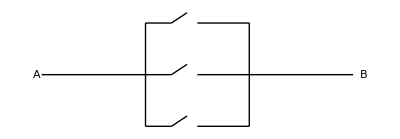

```mathematica
Graphics[{Line[{{0,1},{2,1}}],Line[{{4,1},{6,1}}],Line[{{2,0},{2,2}}],Line[{{4,0},{4,2}}],Line[{{2,2},{2.5,2}}],Line[{{2,1},{2.5,1}}],Line[{{2,0},{2.5,0}}],Line[{{3,2},{4,2}}],Line[{{3,1},{4,1}}],Line[{{3,0},{4,0}}],Line[{{2.5,2},{2.8,2.2}}],Line[{{2.5,1},{2.8,1.2}}],Line[{{2.5,0},{2.8,0.2}}],
Text[Style[A,Large],{-0.1,1}],Text[Style[B,Large],{6.2,1}]}]
```

Figure 1.14 - A parallel circuit

Current coming from point A may reach point B if and only if at least one of the switches is closed.  If the switches act independently of one another, and they have probabilities p_1, p_2, and p_3 of being closed, what is the probability that current will flow?
	This is an easy one.  The event that current will flow is the complement of the event that it will not flow.  The latter happens if and only if all three switches are open.  Switch i is open with probability 1-p_i.  Thus, by independence,

P[current flows] = 1 - P[current doesn't] = 1-(1-p_1)(1-p_2)(1-p_3)  ■

Example 5  Our last example of this section again deals with simulation and contingency tables.  A good pseudo-random number generator as described in Section 3 ought to have the property that each pseudo-random number that is generated appears to be independent of its predecessors (even though it is of course a deterministic function of its immediate predecessor).  Checking for validity of the generator therefore requires a check for independence of each member from each other in a stream of numbers.  There are several ways to do this, and here is one that is sensitive to unwanted upward or downward trends in the stream of numbers.
	We can be alerted to a possible violation of independence if some property that independence implies is contradicted by the data.  For example, in a stream of 40 numbers we can classify each number according to two characteristics: whether it is in the first group of 20 or the second, and whether it is above some fixed cutoff or below it.  If the numbers are truly random and independent of one another, the group that a number is in should have no effect on whether that number is above or below the cutoff.  If the two-by-two contingency table that we generate in this way shows serious departures from the tallies that we would expect under independence, then the assumption of independence is in doubt.
	Here is a stream of 40 random integers between 1 and 20, simulated using DrawIntegerSample.

```mathematica
Needs["KnoxProb7`Utilities`"];
SeedRandom[11753];
datalist=DrawIntegerSample[1,20,40,Replacement->True]
```

{16,9,7,3,3,3,15,17,1,6,3,6,19,18,1,6,2,12,12,18,7,13,2,14,10,20,1,16,14,14,9,13,4,8,15,4,15,9,1,14}

Among the first 20 numbers, 12 are less than or equal to 10 and 8 are greater than 10. Among the second group of 20 numbers, 10 are less than or equal to 10 and 10 are greater.  We therefore have the following observed contingency table.

|   | size  |   |  
  |   | ≤10 | >10 | total
group | 1 | 12 | 8 | 20
  | 2 | 10 | 10 | 20
  | total | 22 | 18 | 40

Equal numbers of 10 observations are to be expected in each category. Interestingly, this particular table is coming very close to independence, because the fact that the row totals are 20 means that the 22 and 18 observations in the two columns should split about evenly between the two rows, which they do.  There is very little evidence against independence in this run of the experiment.  ■

Activity 3  Repeat the drawing of a sample of 40 from {1,2, ...,20} a few more times.  Do you observe many tables that are far from expectations?  Try doubling the sample size to 80, and using four groups of 20 instead of two.  What category counts are expected?  Do you see striking departures from them in your simulations?

### Exercises 1.6

1.  A student guesses randomly on ten multiple choice quiz questions with five alternative answers per question.  Assume that there is only one correct response to each question, and the student chooses answers independently of other questions.  What is the probability that the student gets no more than one question right?

2.  Consider the experiment of randomly sampling a single number from {1,2, ...,10}.  Is the event that the number is odd independent of the event that it is greater than 4?

3.  If A and B are independent events, prove that each of the following pairs of events are independent of one another: (a) A and B^c;  (b) A^c and B;  (c) A^c and B^c.

4.  If events A and B have positive probability and are disjoint, is it possible for them to be independent?

5.  Prove that if events A, B, C, and D are independent of one another, then so are the groups of events (a) A, B, and C; (b) A and B.

6.  Prove that both Ω and ∅ are independent of every other event A⊂Ω.

7.  (Mathematica)  Referring to Example 3, run the SimContingencyTable command a few times each for sample sizes of 40, 80, and 120.  Compare the variabilities for the three sample sizes.

8.  A sample space has six outcomes: a, b, c, d, e, and f.  Define the event A as {a,b,c,d} and the event B as {c,d,e,f}.  If each of a, b, e, and f has probability 1/8, find probabilities on c and d that make A and B independent events, or explain why it is impossible to do so.

9.  Three coins are flipped in succession.  
  (a) If outcomes are equally likely, show that "H on 1st" is independent of "T on 2nd" and show that "H on 2nd" is independent of "T on 3rd." 
  (b) Put probabilities on the sample space consistent with the assumptions of independence of different flips and an unfair weighting such that tails is 51% likely to occur on a single flip.

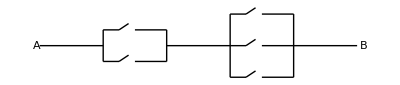

```mathematica
Graphics[{Line[{{0,1},{2,1}}],Line[{{4,1},{6,1}}],Line[{{-4,1},{-2,1}}],Line[{{2,0},{2,2}}],Line[{{4,0},{4,2}}],Line[{{-2,0.5},{-2,1.5}}],Line[{{0,0.5},{0,1.5}}],Line[{{2,2},{2.5,2}}],Line[{{2,1},{2.5,1}}],Line[{{2,0},{2.5,0}}],Line[{{3,2},{4,2}}],Line[{{3,1},{4,1}}],Line[{{3,0},{4,0}}],Line[{{-2,0.5},{-1.5,0.5}}],Line[{{-2,1.5},{-1.5,1.5}}],Line[{{-1,0.5},{0,0.5}}],Line[{{-1,1.5},{0,1.5}}],Line[{{2.5,2},{2.8,2.2}}],Line[{{2.5,1},{2.8,1.2}}],Line[{{2.5,0},{2.8,0.2}}],Line[{{-1.5,1.5},{-1.2,1.7}}],Line[{{-1.5,0.5},{-1.2,0.7}}],
Text[Style[A,Large],{-4.1,1}],Text[Style[B,Large],{6.2,1}]}]
```

Exercise 10

10.  In the figure is a part of an electrical circuit as in Example 4, except that two parallel groups of switches are connected in series.  Current must pass through both groups of switches to flow from A to B.  If each switch in the first group has probability p of being closed, each switch in the second group has probability q of being closed, and the switches operate independently, find the probability that current will flow from A to B.

11.  (Mathematica)  A system has three independent components which work for a random, uniformly distributed amount of time in [10,20] and then fail.  Each component can take on the workload of the other, so the system fails when the final component dies.  Simulate 1000 such systems, produce a histogram of the system failure times, and estimate the probability that the system fails by time 15.  What is the exact value of that probability?

12.  In Example 4 we were able to find the probability that current flows from A to B easily by complementation.  Compute the same probability again without complementation.

13.  (Mathematica)  In Example 5 we set up the integer sampling process so that replacement occurs.  If the pseudo-random number generator behaves properly we would not expect any evidence against randomness.  But the question arises: is this test sensitive enough to detect real independence problems?  Try drawing integer samples again, this time of 40 integers from {1,2,...,80} without replacement.  Using characteristics of group (1st 20, 2nd 20) and size (40 or below, more than 40), simulate some contingency tables to see whether you spot any clear departures from independence.  Would you expect any?

14.  If events B_1, B_2, B_3, and B_4 are independent, show that 
  (a) P[B_1 | B_3∩B_4] = P[B_1]
  (b) P[B_1∩B_2 | B_3∩B_4] = P[B_1∩B_2]
  (c) P[B_1∪B_2 | B_3] = P[B_1∪B_2]

15. A stock goes up or down from one day to another independently.  Each day the probability that it goes up is .4.  Find the probability that in a week of five trading days the stock goes up at least four times.

16.  Two finite or countable families of events A = {A_1,A_2,... } and  B = {B_1,B_2,... } are called independent if every event A_i ∈ A is independent of every event B_j ∈ B.  Suppose that two dice are rolled one after the other.  Let A consist of basic events of the form "1st die = n" for n = 1, 2, ..., 6, together with all unions of such basic events.  Similarly let B be the events that pertain to the second die.  Show that each basic event in A is independent of each basic event in B, and use this to show that the families A and B are independent.

Sample Problem from Actuarial Exam P

17.  An actuary studying the insurance preferences of automobile owners makes the following conclusions: (i) an automobile owner is twice as likely to purchase collision coverage as disability coverage; (ii) the event that an automobile owner purchases collision coverage is independent of the event that he or she purchases disability coverage; (iii) the probability that an automobile owner purchases both collision and disability coverages is .15. What is the probability that an automobile owner purchases neither collision nor disability coverage?